```mathematica
(* Copyright 2013 Thomas Trogdon *)
(* This software is distributed under the terms of the GNU General Public License *)
```

```mathematica
Quit[]
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`myNLS`;
<<ISTPackage`Common`;
```

### Test cauchy transform for the case of x<=-t (special cases of insufficient points?)

```mathematica
ν=0.02;
nu1=Sqrt[1/(8ν)^2-(1/(8ν)-ν)^2];
ρ1[k_]:=k^4/(1+k^8);
ρ1[k_]:=1*Abs[k]^4/(1+Exp[6*Sqrt[Abs[k]]]);
τ1[k_]:=1+ ρ1[k]cc[ρ1[cc[k]]];
bigN=200;
el=60.;
ρ1[el]
ift=Fun[Log[τ1[#]]&,{-el,0}//Line,bigN];
iftb=Fun[Log[τ1[#]]&,{0,el}//Line,bigN];
deltat[k_]:=Exp[(Cauchy[ift,k]+Cauchy[iftb,k])];
r4=Fun[deltat[#]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
iftc=Fun[Log[τ1[#]]&,{-el,el}//Line,2*bigN];
r5=Fun[Exp[Cauchy[iftc,#]]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
r6=Fun[Exp[(Cauchy[ift,#])]&,Line[{-el-I*ν,-nu1-I*ν}],bigN];
```

8.4805×10^-14

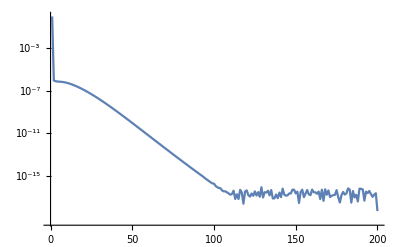
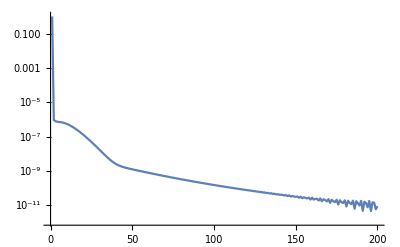
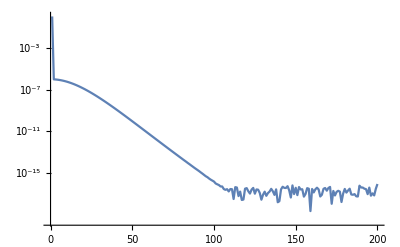

```mathematica
DCTPlot/@{r4,r5,r6}
```

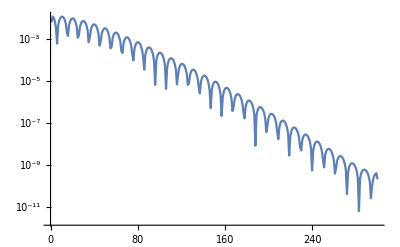
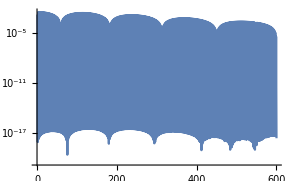

```mathematica
DCTPlot/@{ift,iftc}
```

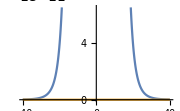

```mathematica
iftc
```

### Test mappings

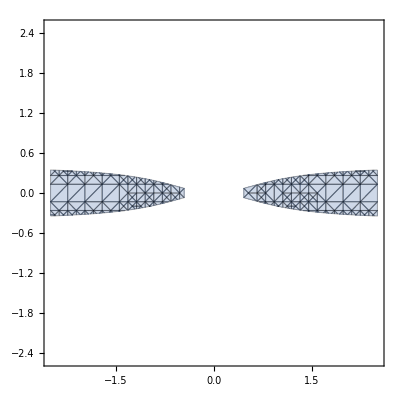
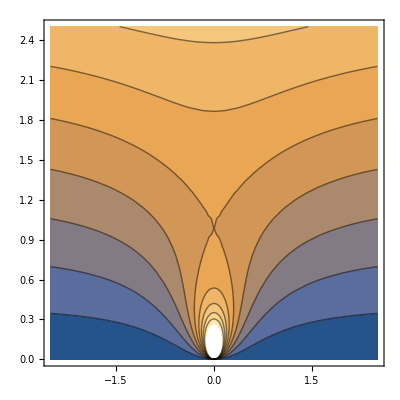

```mathematica
w[x_,y_]:=(x+I y-1/(x+I y))/4;
w[x_,y_]:=(x+I y-1/(x+I y))/4;
xlim=2.5;
ylim=2.5;
{RegionPlot[Abs[Im[w[x,y]]]<0.1,{x,-xlim,xlim},{y,-ylim,ylim},Mesh->All],
ContourPlot[Abs[Im[w[x,y]]],{x,-xlim,xlim},{y,0,ylim},PlotRange->{0,1}]}
```

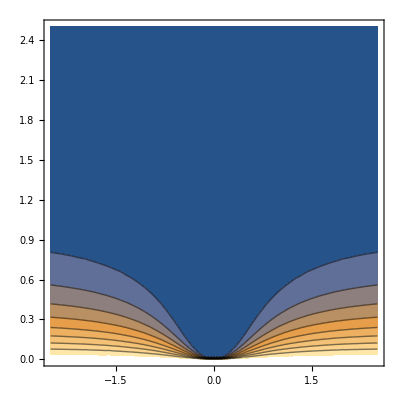

```mathematica
ContourPlot[Abs[Exp[I*w[x,y]*10]],{x,-xlim,xlim},{y,0,ylim},PlotRange->{0,0.9}]
```

```mathematica
ComplexExpand[w[x,y]]
```

x/4-x/(4 (x^2+y^2))+ⅈ (y/4+y/(4 (x^2+y^2)))

```mathematica
RegionPlot[y/4+y/(4 (x^2+y^2))<0.1]
```

0.489898

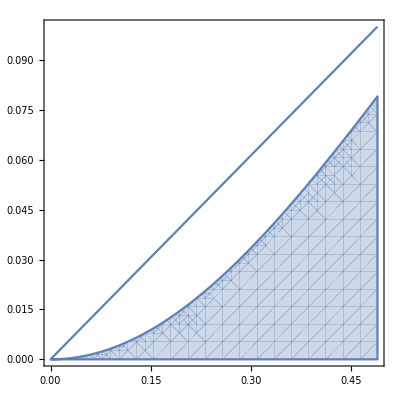

```mathematica
nu=0.1;
nu1=Sqrt[1/(8nu)^2-(1/(8nu)-nu)^2]
Show[{RegionPlot[y/4+y/(4 (x^2+y^2))<nu,{x,0,nu1},{y,0,nu}],Plot[nu/nu1 x,{x,0,nu1}]}]
```

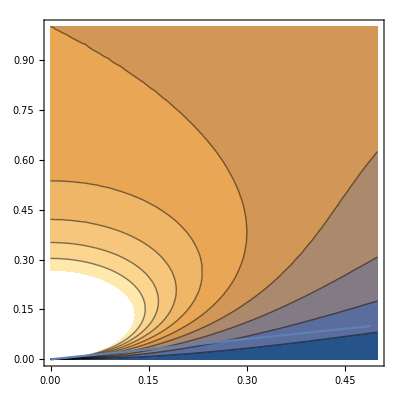

```mathematica
Show[{ContourPlot[Abs[Im[w[x,y]]],{x,0,0.5},{y,0,1},PlotRange->{0,1}],Plot[nu/nu1 x,{x,0,nu1}]}]
```

```mathematica
theta[a_,b_]:=2*I/4*((a+I b-1/(a+I b))*x/t+(a+I b+1/(a+I b)));
ComplexExpand[theta[a,b]*t]
```

-(b t)/2+(b t)/(2 (a^2+b^2))-(b x)/2-(b x)/(2 (a^2+b^2))+ⅈ ((a t)/2+(a t)/(2 (a^2+b^2))+(a x)/2-(a x)/(2 (a^2+b^2)))

```mathematica
theta[a_,b_]:=((a+I b-1/(a+I b)));
ComplexExpand[theta[a,b]]
```

a-a/(a^2+b^2)+ⅈ (b+b/(a^2+b^2))

```mathematica
ComplexExpand[Simplify[theta[a,k*a]]]
```

-(a k)/2+k/(2 a (1+k^2))-(a k x)/(2 t)-(k x)/(2 a (1+k^2) t)+ⅈ (a/2+1/(2 a (1+k^2))+(a x)/(2 t)-x/(2 a (1+k^2) t))

```mathematica
ff[a_]:=Exp[2*I*t*theta[a,1*a]];
Integrate[ff[a]^2,{a,0,Infinity}]
```

ConditionalExpression[(2 BesselK[1,(4 √((1+ⅈ) (t+x)))/(√((1+ⅈ)/(t-x)))])/(√((1+ⅈ)/(t-x)) √((1+ⅈ) (t+x))),(Im[t]+Im[x]+Re[t]+Re[x]==0&&Im[x]+Re[x]<0&&Re[t]+Re[x]>0)||(Re[(1-ⅈ) (t-x)]>0&&Re[(1+ⅈ) (t+x)]>0&&Re[(2+2 ⅈ) (t+x)]≥0&&((Re[(-2-2 ⅈ) (t+x)]==0&&Re[(-1+ⅈ) (t-x)]<0)||Re[(-2-2 ⅈ) (t+x)]<0))]

```mathematica
Kdv
ComplexExpand[2*I*(4*t*(a+b I)^3+x*(a+b I))]
```

Kdv

-24 a^2 b t+8 b^3 t-2 b x+ⅈ (8 a^3 t-24 a b^2 t+2 a x)

```mathematica
NLS
ComplexExpand[2*I*(2*t*(a+b I)^2+x*(a+b I))]
```

NLS

-8 a b t-2 b x+ⅈ (4 a^2 t-4 b^2 t+2 a x)

### Test deformation: this shows the deformation should be valid

```mathematica
RHSolved//Clear;
RHSolved[X_]:=RHSolved[X]=RHSolve[X];
RHSolution[X_][z_]:=Cauchy[X//RHSolved,z]+IdentityMatrix[2];
```

```mathematica
g[x_]:={{1+1/(x+I)^4,0},{0,1+1/(x+I)^4}};
G={Fun[g,Line[{-100,0}],100],Fun[g,Line[{0,100}],100]};
g[100.][[1,1]]
```

1.-3.998×10^-10 ⅈ

```mathematica
sol[z_]:=RHSolution[G][z][[1,1]];
```

```mathematica
zz=10;
sol[zz+I*0.0000000001]
sol[zz-I*0.0000000001]*g[zz][[1,1]]
```

1.00013-6.70774×10^-6 ⅈ

1.00011-0.0000815845 ⅈ

```mathematica
zz=I+1;
sol[zz]-(1+1/(zz+I)^4)
```

-1.64489×10^-6-9.69732×10^-7 ⅈ

```mathematica
g[x_]:={{1+1/(x+I)^4,0},{0,1+1/(x+I)^4}};
m[x_]:={{(x+I)^4+1,0},{0,(x+I)^4+1}};
p[x_]:={{1/(x+I)^4,0},{0,1/(x+I)^4}};
J1=Fun[g,Line[{-100,-1}],100];
J2=Fun[m,Line[{-1,-I}],100];J3=Fun[m,Line[{-I,1}],100];J4=Fun[p,Line[{-1,I}],100];J5=Fun[p,Line[{I,1}],100];
J6=Fun[g,Line[{1,100}],100];
J={J1,J2,J3,J4,J5,J6};
```

```mathematica
Simplify[m[x].p[x]-g[x]]
```

{{0,0},{0,0}}

```mathematica
sol2[z_]:=RHSolution[J][z][[1,1]];
```

```mathematica
zz=5;
sol2[zz+I*0.0000000001]
sol2[zz-I*0.0000000001]*g[zz][[1,1]]
```

1.00104-0.00105038 ⅈ

1.00104-0.00105039 ⅈ

```mathematica
zz=2I+2;
sol2[zz]-(1+1/(zz+I)^4)
```

1.31377×10^-11+1.01511×10^-11 ⅈ

```mathematica
sol[0.5I]
sol2[0.5I]
```

1.19753-4.16334×10^-17 ⅈ

6.0625-2.57572×10^-14 ⅈ

```mathematica
sol[-1.5I]
sol2[-1.5I]
```

1.+1.38778×10^-17 ⅈ

1.-1.06859×10^-15 ⅈ

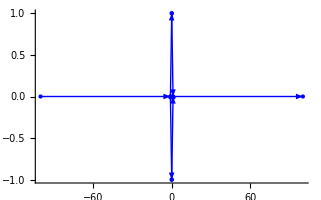

```mathematica
J//DomainPlot
```

### Test deformation: a more complicated version (non commutative matters?)

```mathematica
RHSolved//Clear;
RHSolved[X_]:=RHSolved[X]=RHSolve[X];
RHSolution[X_][z_]:=Cauchy[X//RHSolved,z]+IdentityMatrix[2];
```

```mathematica
r[x_]:=Abs[x]^2*Sech[Abs[x]^2];
g[x_]:={{1+r[x]^2,r[x]},{r[x],1}};
G=Fun[g,Line[{-10,10}],200];
g[10.]
```

{{1.,7.44015×10^-42},{7.44015×10^-42,1}}

```mathematica
sol[z_]:=RHSolution[G][z];
```

```mathematica
zz=1.1;
sol[zz+I*0.0000000001]-sol[zz-I*0.0000000001].g[zz]
```

{{3.97286×10^-7+1.35941×10^-7 ⅈ,9.26294×10^-8+2.62465×10^-8 ⅈ},{-1.29974×10^-7+5.23159×10^-8 ⅈ,-3.359×10^-7+1.18548×10^-7 ⅈ}}

```mathematica
g[x_]:={{1+r[x]^2,r[x]},{r[x],1}};
m[x_]:={{1,r[x]},{0,1}};
im[x_]:=Inverse[m[x]];
p[x_]:={{1,0},{r[x],1}};
ip[x_]:=Inverse[p[x]];
J1=Fun[g,Line[{-10,-1}],100];
J2=Fun[m,Line[{-1,-I}],100];J3=Fun[m,Line[{-I,1}],100];J4=Fun[p,Line[{-1,I}],100];J5=Fun[p,Line[{I,1}],100];
J6=Fun[g,Line[{1,10}],100];
J={J1,J2,J3,J4,J5,J6};
J1[-10]
```

{{1.,7.44015×10^-42},{7.44015×10^-42,1}}

```mathematica
Simplify[m[x].p[x]]
g[x]
```

{{1+Abs[x]^4 Sech[Abs[x]^2]^2,Abs[x]^2 Sech[Abs[x]^2]},{Abs[x]^2 Sech[Abs[x]^2],1}}

{{1+Abs[x]^4 Sech[Abs[x]^2]^2,Abs[x]^2 Sech[Abs[x]^2]},{Abs[x]^2 Sech[Abs[x]^2],1}}

```mathematica
sol2[z_]:=RHSolution[J][z];
```

```mathematica
zz=2.;
Norm[sol2[zz+I*0.00000000001]-sol2[zz-I*0.00000000001].g[zz]]
zz=(1+I)/2.;
Norm[sol2[zz+I*0.00000000001]-sol2[zz-I*0.00000000001].p[zz]]
zz=(1-I)/2.;
Norm[sol2[zz+I*0.00000000001]-sol2[zz-I*0.00000000001].m[zz]]
```

6.50557×10^-7

3.40254×10^-8

3.40254×10^-8

```mathematica
sol[1+1.5I]-sol2[1+1.5I]
```

{{-0.0143675-0.0115041 ⅈ,-0.0358672-0.0230305 ⅈ},{-0.034181-0.0237025 ⅈ,0.00770169+0.00275772 ⅈ}}

```mathematica
sol[-1.5I]-sol2[-1.5I]
```

{{0.00890103-1.11519×10^-18 ⅈ,0.0528469-5.97902×10^-18 ⅈ},{0.0498506+2.39516×10^-17 ⅈ,-0.0224576-1.08326×10^-17 ⅈ}}

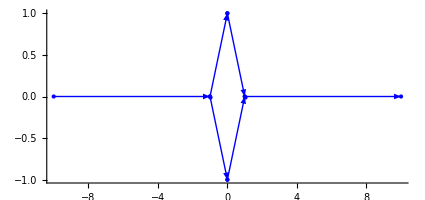

```mathematica
J//DomainPlot
```

```mathematica
r[x_]:=Abs[x]^2*Sech[x];
r1[x_]:=x^2*Sech[x];
g[x_]:={{1+r[x]^2,r[x]},{r[x],1}};
m[x_]:={{1,r[x]},{0,1}};
im[x_]:=Inverse[m[x]];
p[x_]:={{1,0},{r[x],1}};
ip[x_]:=Inverse[p[x]];
H1=Fun[g,Line[{-1,1}],100];
H2=Fun[im,Line[{-1,-I}],100];H3=Fun[im,Line[{-I,1}],100];H4=Fun[ip,Line[{-1,I}],100];H5=Fun[ip,Line[{I,1}],100];
H={H1,H2,H3,H4,H5};
```

```mathematica
sol3[z_]:=RHSolution[H][z];
```

```mathematica
sol3[-0.5I]-im[-0.5I]
```

{{-0.0292075+3.32702×10^-18 ⅈ,-0.295785-2.08167×10^-17 ⅈ},{0.151598+1.92929×10^-18 ⅈ,-0.0605889-2.60209×10^-18 ⅈ}}

```mathematica
sol3[2]
sol3[2I]
```

{{0.998567+0.0132453 ⅈ,-0.00123915-0.051839 ⅈ},{0.00123915-0.051839 ⅈ,0.998567-0.0132453 ⅈ}}

{{1.01447+1.38778×10^-17 ⅈ,-0.049861-2.63177×10^-16 ⅈ},{-0.0580935-6.93889×10^-17 ⅈ,0.988589-9.10323×10^-18 ⅈ}}

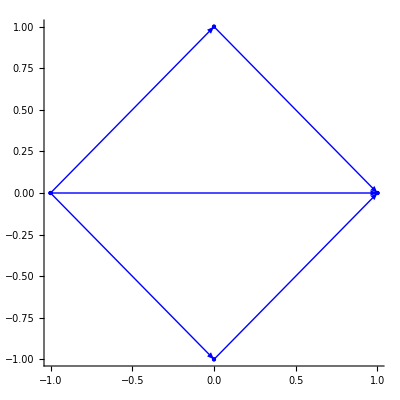

```mathematica
H//DomainPlot
```

```mathematica
H//mRHWellPosed
```

((1. | 0
0 | 1.) | -1.
(1. | 0
0 | 1.) | 0.-1. ⅈ
(1. | 0
0 | 1.) | 0.+1. ⅈ
(1. | 0
0 | 1.) | 1.)

Transformation to get rid of the pole

```mathematica
v[z_,x_]:={{v1[z,x]},{v2[z,x]}};
k[z_]:=1/4(z-1/z);
sigma1={{0,1},{1,0}};
sigma2={{0,-I},{I,0}};
sigma3={{1,0},{0,-1}};
Qp=Sin[u[t,x]/2]*(sigma1*Cos[u[t,x]/2]-sigma3*Sin[u[t,x]/2]);
pp=1/4*(D[u[t,x],t]+D[u[t,x],x]);
Q=-pp*sigma2+Qp/2/z;
```

```mathematica
w[z_,x_]:=(IdentityMatrix[2]*Cos[u[t,x]/2]+I*sigma2*Sin[u[t,x]/2]).v[z,x];
ww[z_,x_]:={{w1[z,x]},{w2[z,x]}};
pm=1/4*(D[u[t,x],x]-D[u[t,x],t]);
R=pm*sigma2+sigma1.Qp.sigma1*z/2;
```

```mathematica
ans0=MatrixForm[FullSimplify[I*D[w[z,x],x]+R.w[z,x]-k[z]*sigma3.w[z,x]]]
```

((Sin[1/2 u[t,x]] ((1+z^2) v2[z,x]-ⅈ z (-4 v2^(0,1)[z,x]+v1[z,x] (u^(0,1)[t,x]+u^(1,0)[t,x])))+Cos[1/2 u[t,x]] (-(-1+z^2) v1[z,x]+ⅈ z (4 v1^(0,1)[z,x]+v2[z,x] (u^(0,1)[t,x]+u^(1,0)[t,x]))))/(4 z)
(Cos[1/2 u[t,x]] ((-1+z^2) v2[z,x]-ⅈ z (-4 v2^(0,1)[z,x]+v1[z,x] (u^(0,1)[t,x]+u^(1,0)[t,x])))+Sin[1/2 u[t,x]] ((1+z^2) v1[z,x]-ⅈ z (4 v1^(0,1)[z,x]+v2[z,x] (u^(0,1)[t,x]+u^(1,0)[t,x]))))/(4 z))

```mathematica
ans1=MatrixForm[FullSimplify[I*D[ww[z,x],x]+R.ww[z,x]-k[z]*sigma3.ww[z,x]]]
```

(((1-z^2 Cos[u[t,x]]) w1[z,x]+z (4 ⅈ w1^(0,1)[z,x]+w2[z,x] (z Sin[u[t,x]]-ⅈ u^(0,1)[t,x]+ⅈ u^(1,0)[t,x])))/(4 z)
((-1+z^2 Cos[u[t,x]]) w2[z,x]+4 ⅈ z w2^(0,1)[z,x]+z w1[z,x] (z Sin[u[t,x]]+ⅈ (u^(0,1)[t,x]-u^(1,0)[t,x])))/(4 z))

```mathematica
Assuming[((-1+z^2 Cos[u[t,x]]) w2[z,x]+4 ⅈ z Derivative[0,1][w2][z,x]+z w1[z,x] (z Sin[u[t,x]]+ⅈ (Derivative[0,1][u][t,x]-Derivative[1,0][u][t,x])))/(4 z),z≠0]
```

((-1+z^2 Cos[u[t,x]]) w2[z,x]+4 ⅈ z w2^(0,1)[z,x]+z w1[z,x] (z Sin[u[t,x]]+ⅈ (u^(0,1)[t,x]-u^(1,0)[t,x])))/(4 z)

```mathematica
FullSimplify[ReplaceAll[ans0,{Derivative[0,1][v1][z,x]->((k[z]*sigma3.v[z,x]-Q.v[z,x])/I)[[1,1]],Derivative[0,1][v2][z,x]->((k[z]*sigma3.v[z,x]-Q.v[z,x])/I)[[2,1]]}]]//MatrixForm
```

(0
0)

Compute real part of theta

```mathematica
z=r Exp[ I w]
z1=a+I b
Assuming[a∈Reals&&b∈Reals,Re[z]]
```

ⅇ^(ⅈ w) r

a+ⅈ b

Re[ⅇ^(ⅈ w) r]

```mathematica
Simplify[Im[I*((z+1/z)*t+(z-1/z)*x)], Element[a, Reals]&&Element[b, Reals]&&Element[x, Reals]&&Element[t, Reals]]
```

Re[(ⅇ^(-ⅈ w) (t+ⅇ^(2 ⅈ w) r^2 t+(-1+ⅇ^(2 ⅈ w) r^2) x))/r]

```mathematica
Simplify[Re[1/z], Element[a, Reals]&&Element[b, Reals]&&Element[x, Reals]&&Element[t, Reals]]
```

Re[ⅇ^(-ⅈ w)/r]

```mathematica
re=ComplexExpand[Re[I*((z+1/z)*t+(z-1/z)*x)]]
```

(t Sin[w])/r-r t Sin[w]-(x Sin[w])/r-r x Sin[w]

```mathematica
im=ComplexExpand[Im[I*((z+1/z)*t+(z-1/z)*x)]]
```

(t Cos[w])/r+r t Cos[w]-(x Cos[w])/r+r x Cos[w]

```mathematica
re1=ComplexExpand[Re[I*((z1+1/z1)*t+(z1-1/z1)*x)]]
```

-b t+(b t)/(a^2+b^2)-b x-(b x)/(a^2+b^2)

```mathematica
im1=ComplexExpand[Im[I*((z1+1/z1)*t+(z1-1/z1)*x)]]
```

a t+(a t)/(a^2+b^2)+a x-(a x)/(a^2+b^2)

Transformation to get rid of the pole

```mathematica
v[z_,x_]:={{v1[z,x]},{v2[z,x]}};
k[z_]:=1/4(z-1/z);
sigma1={{0,1},{1,0}};
sigma2={{0,-I},{I,0}};
sigma3={{1,0},{0,-1}};
Qp=Sin[u[t,x]/2]*(sigma1*Cos[u[t,x]/2]-sigma3*Sin[u[t,x]/2]);
pp=1/4*(D[u[t,x],t]+D[u[t,x],x]);
Q=-pp*sigma2+Qp/2/z;
```

```mathematica
w[z_,x_]:=(IdentityMatrix[2]*Cos[u[t,x]/2]+I*sigma2*Sin[u[t,x]/2]).v[z,x];
ww[z_,x_]:={{w1[z,x]},{w2[z,x]}};
pm=1/4*(D[u[t,x],x]-D[u[t,x],t]);
R=pm*sigma2+sigma1.Qp.sigma1*z/2;
```

```mathematica
ans0=MatrixForm[FullSimplify[I*D[w[z,x],x]+R.w[z,x]-k[z]*sigma3.w[z,x]]]
```

((Sin[1/2 u[t,x]] ((1+z^2) v2[z,x]-ⅈ z (-4 v2^(0,1)[z,x]+v1[z,x] (u^(0,1)[t,x]+u^(1,0)[t,x])))+Cos[1/2 u[t,x]] (-(-1+z^2) v1[z,x]+ⅈ z (4 v1^(0,1)[z,x]+v2[z,x] (u^(0,1)[t,x]+u^(1,0)[t,x]))))/(4 z)
(Cos[1/2 u[t,x]] ((-1+z^2) v2[z,x]-ⅈ z (-4 v2^(0,1)[z,x]+v1[z,x] (u^(0,1)[t,x]+u^(1,0)[t,x])))+Sin[1/2 u[t,x]] ((1+z^2) v1[z,x]-ⅈ z (4 v1^(0,1)[z,x]+v2[z,x] (u^(0,1)[t,x]+u^(1,0)[t,x]))))/(4 z))

```mathematica
ans1=MatrixForm[FullSimplify[I*D[ww[z,x],x]+R.ww[z,x]-k[z]*sigma3.ww[z,x]]]
```

(((1-z^2 Cos[u[t,x]]) w1[z,x]+z (4 ⅈ w1^(0,1)[z,x]+w2[z,x] (z Sin[u[t,x]]-ⅈ u^(0,1)[t,x]+ⅈ u^(1,0)[t,x])))/(4 z)
((-1+z^2 Cos[u[t,x]]) w2[z,x]+4 ⅈ z w2^(0,1)[z,x]+z w1[z,x] (z Sin[u[t,x]]+ⅈ (u^(0,1)[t,x]-u^(1,0)[t,x])))/(4 z))

```mathematica
Assuming[((-1+z^2 Cos[u[t,x]]) w2[z,x]+4 ⅈ z Derivative[0,1][w2][z,x]+z w1[z,x] (z Sin[u[t,x]]+ⅈ (Derivative[0,1][u][t,x]-Derivative[1,0][u][t,x])))/(4 z),z≠0]
```

((-1+z^2 Cos[u[t,x]]) w2[z,x]+4 ⅈ z w2^(0,1)[z,x]+z w1[z,x] (z Sin[u[t,x]]+ⅈ (u^(0,1)[t,x]-u^(1,0)[t,x])))/(4 z)

```mathematica
FullSimplify[ReplaceAll[ans0,{Derivative[0,1][v1][z,x]->((k[z]*sigma3.v[z,x]-Q.v[z,x])/I)[[1,1]],Derivative[0,1][v2][z,x]->((k[z]*sigma3.v[z,x]-Q.v[z,x])/I)[[2,1]]}]]//MatrixForm
```

(0
0)

Compute real part of theta

```mathematica
z=r Exp[ I w]
z1=a+I b
Assuming[a∈Reals&&b∈Reals,Re[z]]
```

ⅇ^(ⅈ w) r

a+ⅈ b

Re[ⅇ^(ⅈ w) r]

```mathematica
Simplify[Im[I*((z+1/z)*t+(z-1/z)*x)], Element[a, Reals]&&Element[b, Reals]&&Element[x, Reals]&&Element[t, Reals]]
```

Re[(ⅇ^(-ⅈ w) (t+ⅇ^(2 ⅈ w) r^2 t+(-1+ⅇ^(2 ⅈ w) r^2) x))/r]

```mathematica
Simplify[Re[1/z], Element[a, Reals]&&Element[b, Reals]&&Element[x, Reals]&&Element[t, Reals]]
```

Re[ⅇ^(-ⅈ w)/r]

```mathematica
re=ComplexExpand[Re[I*((z+1/z)*t+(z-1/z)*x)]]
```

(t Sin[w])/r-r t Sin[w]-(x Sin[w])/r-r x Sin[w]

```mathematica
im=ComplexExpand[Im[I*((z+1/z)*t+(z-1/z)*x)]]
```

(t Cos[w])/r+r t Cos[w]-(x Cos[w])/r+r x Cos[w]

```mathematica
re1=ComplexExpand[Re[I*((z1+1/z1)*t+(z1-1/z1)*x)]]
```

-b t+(b t)/(a^2+b^2)-b x-(b x)/(a^2+b^2)

```mathematica
im1=ComplexExpand[Im[I*((z1+1/z1)*t+(z1-1/z1)*x)]]
```

a t+(a t)/(a^2+b^2)+a x-(a x)/(a^2+b^2)

## Test Fourier transform

```mathematica
dt=1;M=128;T=M*dt;g=0.0;p=0.7;w0=0.62;
timeseries:=Table[Exp[-g Abs[t-T/2]]*Sin[w0 t+p],{t,0,M-1}];
```

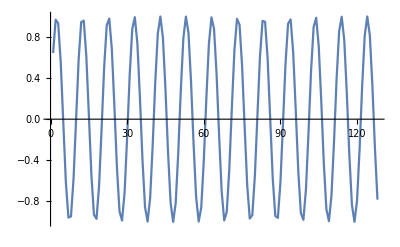

```mathematica
ListPlot[timeseries,Joined->True]
```

```mathematica
InverseFourier[{0,0,0,1}]
```

{0.5+0. ⅈ,0.+0.5 ⅈ,-0.5+0. ⅈ,0.-0.5 ⅈ}

```mathematica
<<FourierSeries`
```

```mathematica
q[x_]:=Sech[x^2];
q0hat[w_]:=NFourierTransform[q[x],x,w];
qthat[w_,t_]:=q0hat[w];
qsmall[x_,t_]:=NInverseFourierTransform[qthat[w,t],w,x];
```

```mathematica
NInverseFourierTransform[qthat[w,t],w,0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {6.3887×10^56}. NIntegrate obtained 2.57552×10^242 and 2.53864×10^242 for the integral and error estimates.

1.02748×10^242

```mathematica
LL=3;dd=1;
nq0=Table[q[x],{x,-LL,LL-dd,dd}];
w=Pi*dd/LL*Join[Range[0,Length[nq0]/2], Range[-Length[nq0]/2+1,-1]];
nhq0=Fourier[nq0];
nhqt=nhq0*w;
```

```mathematica
xx=Range[-LL,LL-dd,dd]
```

{-3,-2,-1,0,1,2}

```mathematica
nq0
```

{Sech[9],Sech[4],Sech[1],1,Sech[1],Sech[4]}

```mathematica
w
```

{0,π/3,(2 π)/3,π,-(2 π)/3,-π/3}

```mathematica
Join[Range[0,Length[nq0]/2], Range[-Length[nq0]/2+1,-1]]
```

{0,1,2,3,-2,-1}

```mathematica
nq0
```

{Sech[9],Sech[4],Sech[1],1,Sech[1],Sech[4],Sech[9]}

```mathematica
w
```

{-(5 π)/6,-π/2,-π/6,π/6,π/2,(5 π)/6,(7 π)/6}

```mathematica
Length[nq0]
```

7

```mathematica
List[1,Length[nq0]]
```

{1,7}

## Test fun

```mathematica
Clear[q];
q[x_]=x;
```

```mathematica
q[2]
```

2

```mathematica
qf=Fun[q,Line[{0,2}],5];
```

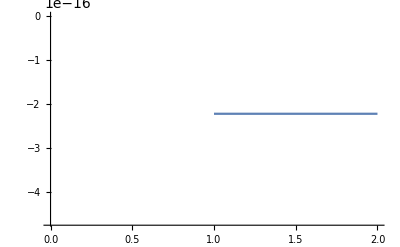

```mathematica
qf//DCTPlot
```

```mathematica
qf//Values
```

{0.,0.292893,1.,1.70711,2.}

```mathematica
dm=DerivativeMatrix[qf]
```

{{-5.5,6.82843,-2.,1.17157,-0.5},{-1.70711,0.707107,1.41421,-0.707107,0.292893},{0.5,-1.41421,0.,1.41421,-0.5},{-0.292893,0.707107,-1.41421,-0.707107,1.70711},{0.5,-1.17157,2.,-6.82843,5.5}}

```mathematica
dm.(qf//Values)
```

{1.,1.,1.,1.,1.}

```mathematica
IIm=ReduceDimensionIntegrateMatrix[qf](*This gives the indefinite integral*)
```

{{0.0125,-0.025,0.025,-0.025,0.0125},{0.110565,0.207741,-0.0419417,0.0309644,-0.0144353},{0.0333333,0.62022,0.4,-0.0868867,0.0333333},{0.0811019,0.502369,0.841942,0.325592,-0.0438981},{0.0541667,0.558333,0.775,0.558333,0.0541667}}

```mathematica
IIm.(qf//Values)-(0.5*qf^2//Values)
```

{-7.66748×10^-16,1.80411×10^-16,-1.11022×10^-16,0.,4.44089×10^-16}

```mathematica
Integrate[qf]//Values
```

{0.,0.0182373,0.238729,0.856763,1.63627,2.}

```mathematica
ReduceDimension[qf]//Values
```

{0.,0.5,1.5,2.}

```mathematica
ReduceDimensionMatrix[qf]
```

{{0.875,0.25,-0.25,0.25,-0.125},{-0.125,0.78033,0.5,-0.28033,0.125},{0.125,-0.28033,0.5,0.78033,-0.125},{-0.125,0.25,-0.25,0.25,0.875}}

```mathematica
IIm.Values[qf]
```

{-7.66748×10^-16,0.0428932,0.5,1.45711,2.}

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
DiagonalMatrix[qf//Values]
```

{{0.,0.,0.,0.,0.},{0.,0.292893,0.,0.,0.},{0.,0.,1.,0.,0.},{0.,0.,0.,1.70711,0.},{0.,0.,0.,0.,2.}}

```mathematica
?ReduceDimensionIntegrateMatrix  
(*"ReduceDimensionIntegrate[ifun] returns the ReduceDimension[Integrate[ifun]].";*)
```

RiemannHilbert`Common`ReduceDimensionIntegrateMatrix

ReduceDimensionIntegrateMatrix[Private`d_?DomainQ,Private`n_Integer]:=ReduceDimensionMatrix[Private`d,Private`n+1].IntegrateMatrix[Private`d,Private`n]
 
ReduceDimensionIntegrateMatrix[Private`f_]:=ReduceDimensionIntegrateMatrix[Domain[Private`f],Length[Private`f]]

## Reflection Coefficient

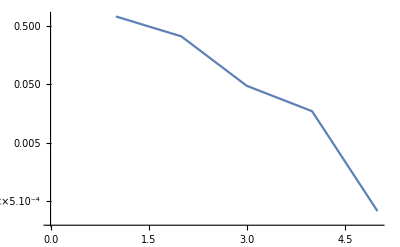
{0.367879,-Graphics-}

```mathematica
Clear[q];
q[x_]=Exp[-x^2];
w=0;
CME[x_]:=Chop[x,$MachineEpsilon];
n=5;el=1;λ=1;
qf=Fun[q,Line[{-el,0}],n];
qfb=Fun[q,Line[{0,el}],n];
Print[{qf//Values//First//Abs,qf//DCTPlot}];
```

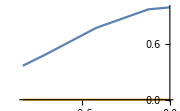

```mathematica
qf=Fun[q,Line[{-el,0}],n]
```

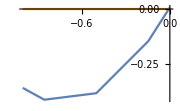

```mathematica
qf=-0.5*qf'
```

```mathematica
Dm=DerivativeMatrix[qf];      (*this gives the chebyshev differentiation matrix*)
Dmb=DerivativeMatrix[qfb];  (*ie   Dm . Values[qf] = derivative of qf *)
IIm=ReduceDimensionIntegrateMatrix[qf];(*This gives the indefinite integral*)
IImb=(ReduceDimensionIntegrateMatrix[(qfb//ReverseOrientation)]//Transpose//Reverse//Transpose//Reverse);
id=IdentityMatrix[n];
Q = DiagonalMatrix[qf//Values];
R= -λ DiagonalMatrix[qf//Conjugate//Values];
Qb = DiagonalMatrix[qfb//Values];
Rb = -λ DiagonalMatrix[qfb//Conjugate//Values];
A=BlockMatrix[{{id,-IIm.Q},{-IIm.R,id}}];
Ab=BlockMatrix[{{id,-IImb.Qb},{-IImb.Rb,id}}];
Jσ3=BlockMatrix[{{0*id,0},{0,-2I IIm}}];
Jσ31=BlockMatrix[{{2I IIm,0},{0,0*id}}];
Jσ3b=BlockMatrix[{{0*id,0},{0,-2I IImb}}];
Jσ31b=BlockMatrix[{{2I IImb,0},{0,0*id}}];
q = qf//Values;
qb = qfb//Values;
r = -λ q//Conjugate;
rb= -λ qb//Conjugate;
n = q//Length;
lhs=A+ w*Jσ3;
rhs = Join[ConstantArray[0.,n],IIm.r];
ans0 = LinearSolve[lhs//CME,rhs//CME];
lhs=A+w*Jσ31;
rhs=Join[IIm.q,ConstantArray[0.,n]];
ans1 = LinearSolve[lhs//CME,rhs//CME];
s1={{ans0[[n]]+1,-ans1[[n]]},{ans0[[2n]],-ans1[[2n]]-1}};
lhs=Ab+ w*Jσ3b;
Off[LinearSolve::luc];
rhs = Join[ConstantArray[0.,n],IImb.rb];
ans0 = LinearSolve[lhs//CME,rhs//CME];
lhs=Ab+ w*Jσ31b;
rhs = Join[IImb.qb,ConstantArray[0.,n]];
ans1 = LinearSolve[lhs//CME,rhs//CME];
On[LinearSolve::luc];
s2={{ans0[[1]]+1,ans1[[1]]},{ans0[[n+1]],ans1[[n+1]]+1}};
s1=Inverse[s2].s1
```

{{0.0768056,-0.997046},{-0.997046,-0.0768056}}

```mathematica
Dimensions[lhs]
Dimensions[rhs]
```

{10,10}

{10}

```mathematica
Dimensions[Dm]
Dimensions[IIm]
```

{5,5}

{5,5}

```mathematica
Dm=DerivativeMatrix[qf];      (*this gives the chebyshev differentiation matrix*)
 (*ie   Dm . Values[qf] = derivative of qf *)
IIm=ReduceDimensionIntegrateMatrix[qf];
id=IdentityMatrix[n];
Q = DiagonalMatrix[qf//Values];
R= -λ DiagonalMatrix[qf//Conjugate//Values];
A=BlockMatrix[{{id,-IIm.Q},{-IIm.R,id}}];

Jσ3=BlockMatrix[{{0*id,0},{0,-2I IIm}}];
Jσ31=BlockMatrix[{{2I IIm,0},{0,0*id}}];
q = qf//Values;
r = -λ q//Conjugate;
n = q//Length;
lhs=A+ w*Jσ3;
rhs = Join[ConstantArray[0.,n],IIm.r];
ans0 = LinearSolve[lhs//CME,rhs//CME];
lhs=A+w*Jσ31;
rhs=Join[IIm.q,ConstantArray[0.,n]];
ans1 = LinearSolve[lhs//CME,rhs//CME];
s1={{ans0[[n]]+1,-ans1[[n]]},{ans0[[2n]],-ans1[[2n]]-1}}
```

{{0.733538,-0.679205},{-0.679205,-0.733538}}

```mathematica
ConstantArray[0.,n]
```

{0.,0.,0.,0.,0.}

## Hill’s method test

```mathematica
mu = .25;
L = Pi;
P =1;
n=5;
Ff[x_]:=Sech[x]/.Underflow[]->0;
t[x_]:=Tan[x/2];
(*f01[x_]:= -I Ff[t[x]];
f02[x_]= -I (-D[Ff[t[x]],x]/2);  (*not delay-set is the key line *)*)
dftx[x_]=D[Ff[t[x]],x];
f02[x_]:= -I (-dftx[x]/2)/.Underflow[]->0;
f01[x_]:=I (dftx[x]/2)/.Underflow[]->0;
mFFT[F_]:=Fourier[F,FourierParameters->{-1,-1}];
InvmFFT[F_]:=InverseFourier[F,FourierParameters->{-1,1}];
FFTShift[V_]:=Module[{n},
n = Length[V]/2;
Join[V[[n+1;;]],V[[1;;n]]]];
FourierCoef[L_,N_,F_]:=Module[{C,p,x,y},
p = 2;
While[p < N, p = 2*p;Print[p];];
x = Table[n, {n, 0.0, 2.0*p - 1}]*L/(p) - L;
Print[x];
y = F[x];
Print[y];
y=Chop[FFTShift[y],$MachineEpsilon];
Print[y];
y = mFFT[y];
C = ConstantArray[0, 2*N + 1];
 C[[1 ;; N + 1]] = y[[1 ;; N + 1]];
      C[[-N ;; -1]] = y[[-N ;; -1]];
       C];
FourierCoef[L,n,f02];
```

4

8

{-3.14159,-2.74889,-2.35619,-1.9635,-1.5708,-1.1781,-0.785398,-0.392699,0.,0.392699,0.785398,1.1781,1.5708,1.9635,2.35619,2.74889}

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

{0,0.+0.0861186 ⅈ,0.+0.298128 ⅈ,0.+0.312397 ⅈ,0.+0.246777 ⅈ,0.+0.171398 ⅈ,0.+0.105635 ⅈ,0.+0.0500314 ⅈ,0.+0. ⅈ,0.-0.0500314 ⅈ,0.-0.105635 ⅈ,0.-0.171398 ⅈ,0.-0.246777 ⅈ,0.-0.312397 ⅈ,0.-0.298128 ⅈ,0.-0.0861186 ⅈ}

{0,0.-0.0500314 ⅈ,0.-0.105635 ⅈ,0.-0.171398 ⅈ,0.-0.246777 ⅈ,0.-0.312397 ⅈ,0.-0.298128 ⅈ,0.-0.0861186 ⅈ,0,0.+0.0861186 ⅈ,0.+0.298128 ⅈ,0.+0.312397 ⅈ,0.+0.246777 ⅈ,0.+0.171398 ⅈ,0.+0.105635 ⅈ,0.+0.0500314 ⅈ}

```mathematica
f02[1]
```

-1/4 ⅈ Sec[x/2]^2 Sech[Tan[x/2]] Tanh[Tan[x/2]]

```mathematica
pp=8;
xx = Table[n, {n, 0.0, 2.0*pp - 1}]*L/(pp) - L
f02[xx]
```

{-3.14159,-2.74889,-2.35619,-1.9635,-1.5708,-1.1781,-0.785398,-0.392699,0.,0.392699,0.785398,1.1781,1.5708,1.9635,2.35619,2.74889}

General::ovfl: Overflow occurred in computation.

{Underflow[],0.+0.0861186 ⅈ,0.+0.298128 ⅈ,0.+0.312397 ⅈ,0.+0.246777 ⅈ,0.+0.171398 ⅈ,0.+0.105635 ⅈ,0.+0.0500314 ⅈ,0.+0. ⅈ,0.-0.0500314 ⅈ,0.-0.105635 ⅈ,0.-0.171398 ⅈ,0.-0.246777 ⅈ,0.-0.312397 ⅈ,0.-0.298128 ⅈ,0.-0.0861186 ⅈ}

```mathematica
Fourier[{0.+0. ⅈ,0.-0.05003141897792386 ⅈ,0.-0.10563483038270562 ⅈ,0.-0.17139791828675266 ⅈ,0.-0.2467771737822865 ⅈ,0.-0.3123973695744284 ⅈ,0.-0.2981280514240936 ⅈ,0.-0.08611855818412723 ⅈ,Underflow[],0.+0.08611855818412693 ⅈ,0.+0.2981280514240936 ⅈ,0.+0.31239736957442815 ⅈ,0.+0.2467771737822865 ⅈ,0.+0.17139791828675272 ⅈ,0.+0.10563483038270562 ⅈ,0.+0.05003141897792386 ⅈ}]
```

Fourier::fftl: Argument «1» is not a non-empty list or rectangular array of numeric quantities.

Fourier[{0.+0. ⅈ,0.-0.0500314 ⅈ,0.-0.105635 ⅈ,0.-0.171398 ⅈ,0.-0.246777 ⅈ,0.-0.312397 ⅈ,0.-0.298128 ⅈ,0.-0.0861186 ⅈ,Underflow[],0.+0.0861186 ⅈ,0.+0.298128 ⅈ,0.+0.312397 ⅈ,0.+0.246777 ⅈ,0.+0.171398 ⅈ,0.+0.105635 ⅈ,0.+0.0500314 ⅈ}]

```mathematica
(*Test function definition*)
Sca[q_]:=Module[{qf},
       qf=2;
Sca[qf,q]
];
```

```mathematica
Sca[qf_,q_][w_]:=Module[{a},
a=IdentityMatrix[qf]*w
];
```

```mathematica
Sca[2,10][20]
```

{{20,0},{0,20}}

```mathematica
(*Test matrix multiplication*)
Ln[k_]:=({{1, 0}, {r[k]/τ[k] Exp[θ[k]], 1}});
DDn[k_]:=({{τ[k], 0}, {0, 1/τ[k]}});
Un[k_]:=({{1, rb[k]/τ[k] Exp[-θ[k]]}, {0, 1}});
```

```mathematica
Ln[k]
```

{{1,0},{(ⅇ^θ[k] r[k])/τ[k],1}}

```mathematica
(*this is equal to g*)
```

```mathematica
Ln[k].DDn[k].Un[k]
```

{{τ[k],ⅇ^(-θ[k]) rb[k]},{ⅇ^θ[k] r[k],1/τ[k]+(r[k] rb[k])/τ[k]}}

```mathematica
(*Check conjugatelist*)
G1[z_]:={{2,0},{0,1}};
G2[z_]:={{2,0},{0,1}};
J={{G1[#]&,G2[#]&},{Arc[0,1.,{0,π}],Arc[0,1.,{π,2π}]},{10,10}};
RP1=MakeListFun[J];
```

```mathematica
J
```

{{G1[#1]&,G2[#1]&},{Arc[0,1.,{0,π}],Arc[0,1.,{π,2 π}]},{10,10}}

```mathematica
(*RP1 is the jump matrix, the following is calculating the first piece, the 1 1 entry evaluated at I *)
RP1[[1]][[1,1]][I]
```

2.+0. ⅈ

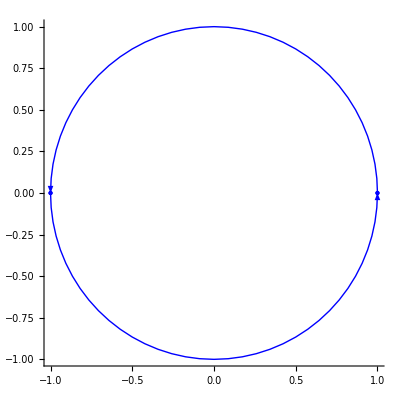

```mathematica
DomainPlot[RP1]
```

```mathematica
RS1=RHSolve[RP1];
RH1Solution[z_]:=Cauchy[RS1,z]+IdentityMatrix[2];
S1[z_]:=Inverse[RH1Solution[z]];
(*the solution is diag 2 1 in the interior and diag 1 1 in the exterior*)
RH1Solution[0]
RH1Solution[2]
```

{{2.+1.49174×10^-17 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.+0. ⅈ}}

{{1.-8.32667×10^-17 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
S1[1]
```

Inverse::inf: Input matrix contains an infinite entry.

Inverse[{{∞,∞},{∞,∞}}]

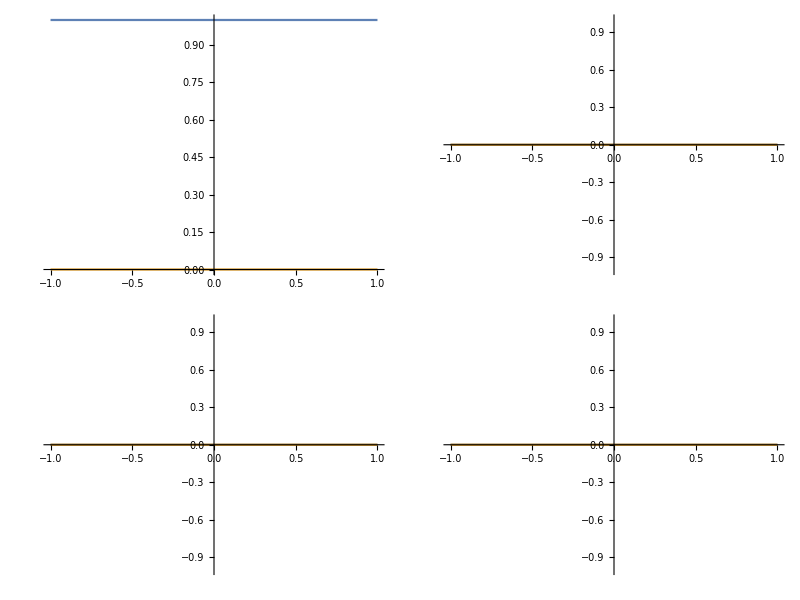
{(-Graphics-),(-Graphics-)}

```mathematica
RS1 (*is the solution obtained after solving the SIE*)
```

```mathematica
Cauchy[RS1,0.99999999]
```

{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

Part::partd: Part specification ∞⟦1,1⟧ is longer than depth of object.

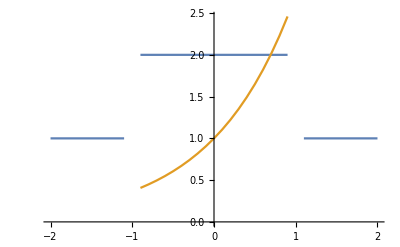

```mathematica
ListLinePlot[{Table[{x,Abs[1+Cauchy[RS1,x]][[1,1]]},{x,-2,2,0.1}],Table[{x,Exp[x]},{x,-0.9,0.9,0.1}]}] (*the warning message comes from the evaluation on the boundary,exp is just for comparison*)
```

```mathematica
JJ=ConjugateList[J,Inverse[S1[#]]&]
```

{{{InvFun[Inverse[S1[#1]]&],G1[#1]&,Inverse[S1[#1]]&}⟦1⟧[#1].{InvFun[Inverse[S1[#1]]&],G1[#1]&,Inverse[S1[#1]]&}⟦2⟧[#1].{InvFun[Inverse[S1[#1]]&],G1[#1]&,Inverse[S1[#1]]&}⟦3⟧[#1]&,{InvFun[Inverse[S1[#1]]&],G2[#1]&,Inverse[S1[#1]]&}⟦1⟧[#1].{InvFun[Inverse[S1[#1]]&],G2[#1]&,Inverse[S1[#1]]&}⟦2⟧[#1].{InvFun[Inverse[S1[#1]]&],G2[#1]&,Inverse[S1[#1]]&}⟦3⟧[#1]&},{Arc[0,1.,{0,π}],Arc[0,1.,{π,2 π}]},{10,10}}

```mathematica
RP2=MakeListFun[JJ]
```

Inverse::inf: Input matrix contains an infinite entry.

General::stop: Further output of Inverse::inf will be suppressed during this calculation.

```mathematica
(*In this case the conjugate does not work because S1 is not defined along the contour. However, in the code, what we want to do is to conjugate with the solution along a different contour which will have a nice value at this contour*)
```

{-Graphics-,-Graphics-}

```mathematica
RP2[[1]][1]
```

Inverse[Inverse[Inverse[{{∞,∞},{∞,∞}}]]].{{2,0},{0,1}}.Inverse[Inverse[{{∞,∞},{∞,∞}}]]

```mathematica
DomainPlot[RP2]
```

-Graphics-

```mathematica
RP2
```

{-Graphics-,-Graphics-}

```mathematica
(*Test adapt in lib.nb*)
J={{G1[#]&,G2[#]&},{Arc[0,1.,{0,π}],Arc[0,1.,{π,2π}]},{10,10}};
```

```mathematica
J[[All,1]]
```

{G1[#1]&,Arc[0,1.,{0,π}],10}

```mathematica
J//Length (*gives number of rows*)
```

3

```mathematica
J//Transpose//Length (*is the number of sections*)
```

2

```mathematica
{{J[[1,1]],J[[2,1]],J[[3,1]]}}//Transpose
```

{{G1[#1]&},{Arc[0,1.,{0,π}]},{10}}

```mathematica
G3[z_]:={{2*z,0},{0,1*z}};
```

```mathematica
J1={{G3[#]&},{Line[{0,2}]},{10}}
```

{{G3[#1]&},{Line[{0,2}]},{10}}

```mathematica
J2={{G3[#]&},{Line[{0,2}][[1]]},{10}}
```

{{G3[#1]&},{{0,2}},{10}}

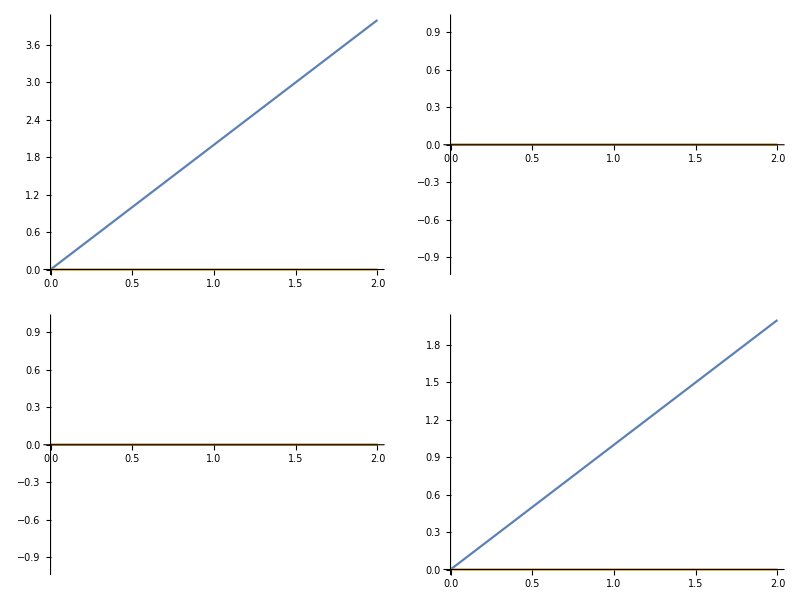
{(-Graphics-)}

```mathematica
R1=MakeListFun[J1]
```

```mathematica
R2=MakeListFun[J2]
```

{Fun[G3[#1]&,0,10],Fun[G3[#1]&,2,10]}

```mathematica
D1[[2]]
```

2.5

```mathematica
FF[z_]:=Exp[-(z-1)^2*2]+Exp[-(z+1)^2*2];
F[z_]:=IdentityMatrix[2]+IdentityMatrix[2]*FF[z];
```

```mathematica
ff[z_]:=Abs[FF[z]]*2;
f[z_]:=IdentityMatrix[2]+IdentityMatrix[2]*ff[z];
```

```mathematica
tol=0.7;
```

```mathematica
J3={{F[#]&,F[#]&},{Line[{-2,2}],Line[{-2+I,2-I}]},{20,20}};
J4={{f[#]&,f[#]&},{Line[{-2,2}],Line[{-2+I,2-I}]},{20,20}};
JJ=Fun[ff[#]&,Line[{-2,2}],50];
```

```mathematica
JJ[-2]
```

0.270671

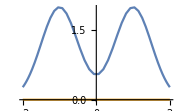

```mathematica
JJ
```

```mathematica
MapFromInterval[Line[{-2,2}],-1]
```

-2

```mathematica
J4[[All,1]]
```

{f[#1]&,Line[{-2,2}],20}

```mathematica
f[z]-IdentityMatrix[2]
```

{{2 Abs[ⅇ^(-2 (-1+z)^2)+ⅇ^(-2 (1+z)^2)],0},{0,2 Abs[ⅇ^(-2 (-1+z)^2)+ⅇ^(-2 (1+z)^2)]}}

```mathematica
TruncateMatrix[tol][J4[[All,1]]]
```

{Line[{-1.7125,-0.2125}],Line[{0.2125,1.7125}]}

```mathematica
out = Table[J4[[All,i]]//TruncateMatrix[tol],{i,1,J4//Transpose//Length}];
```

```mathematica
out
```

{{Line[{-1.7125,-0.2125}],Line[{0.2125,1.7125}]},{Line[{-2+ⅈ,-0.244687+0.122343 ⅈ}],Line[{0.224888-0.112444 ⅈ,2-ⅈ}]}}

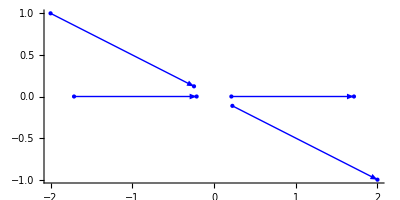

```mathematica
DomainPlot[out]
```

```mathematica
save={{}};
```

```mathematica
For[i=1,i≤Length[out],i++,(*out contains straight line segemnts of the domain that have values larger than the tol*)
For[j=1,j≤Length[out[[i]]],j++,
save = Join[save,{{J3[[1,i]],out[[i,j]],J3[[3,i]]}}//Transpose,2]
(*join 1 means stacking matrix vertically 
  join 2 means stacking matrix horizontally*)
];
];
```

```mathematica
save
```

{{F[#1]&,F[#1]&,F[#1]&,F[#1]&},{Line[{-1.7125,-0.2125}],Line[{0.2125,1.7125}],Line[{-2+ⅈ,-0.244687+0.122343 ⅈ}],Line[{0.224888-0.112444 ⅈ,2-ⅈ}]},{20,20,20,20}}

```mathematica
Join[{A},{B}]
```

{A,B}

## Normal Reflection Coefficient

{0.+1.11151 ⅈ}

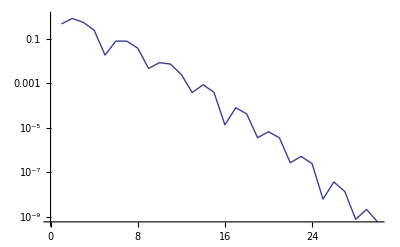
{4.40709×10^-16,-Graphics-}

```mathematica
q[x_]:=1.9 Exp[-x^2]/.Underflow[]->0/.Indeterminate->0.;
q[_?InfinityQ]:=0.    (* PatternTest: q[infinity] gets replaces by 0 *)
Defocusing[];
LocatePolesmKdV[q,40]
H=ScatteringMatrixFinitemKdV[q,30,6];
H[_?InfinityQ]={{1,0},{0,1}};
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];
```

```mathematica
ν=Getnu[];
ρ[k_]:=bb[k]/aa[k];
SetScatteringData[aa,bb,ρ,LocatePolesmKdV[q,40]]
SetParams[.4,.1,10.^(-9),10,20];
h[k_]:=3/(1+Abs[k/2+1/3.2]^8);
Setrsamp[h];
Settimeflag[False];
```

## Cauchy Integral Reflection Coefficient

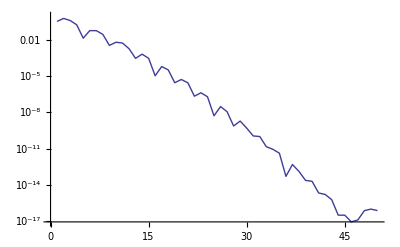
{3.71124×10^-16,-Graphics-}

```mathematica
q[x_]:=1.6Exp[-x^2]/.Underflow[]->0/.Indeterminate->0.;
q[_?InfinityQ]:=0.
Defocusing[];
LocatePolesmKdV[q,40];
H=ScatteringMatrixFinitemKdV[q,50,6];
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];

SetParams[.4,.1,10.^(-9),10,20];
h[k_]:=3/(1+Abs[k/2+1/3.2]^8);
Setrsamp[h];
Settimeflag[False];
ν=Getnu[];
ρ[k_]:=bb[k]/aa[k];
```

```mathematica
up=I(ν+.0001);m=50;el=8;
f={Fun[ρ,Line[{-el,0}-up],2m],Fun[ρ,Line[{0,el}-up],2m],Fun[ρ,Line[{el,0}+up],m],Fun[ρ,Line[{0,-el}+up],m]};
```

```mathematica
mρ//Clear;
mρ[k_]:=mρ[k]=Piecewise[{{Cauchy[f,k], Im[k]< Im[up]}, {ρ[k], True}}];
SetScatteringData[aa,bb,mρ,LocatePolesmKdV[q,40]]

qmKdV//Clear;
qmKdV[x_,t_]:=qmKdV[x,t]=mKdVAuto[x,t];
```

## Plotting: timestring outputs relevant computation times and region information

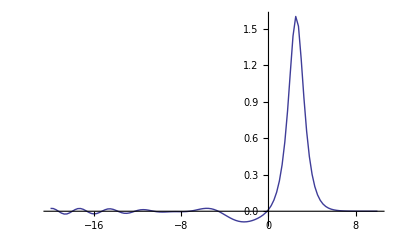

```mathematica
(* Focusing *)
Monitor[TablePlot[qmKdV[x,1.]//Re,{x,-20,10,.25},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

```mathematica
(* Defocusing *)
Monitor[TablePlot[qmKdV[x,1.]//Re,{x,-20,10,.25},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

$Aborted

Function is called in the order of the definition. It returns the first successful evaluation. Only the defition of exactly the same input argument can overwrite the previous definition

```mathematica
choose1[f_?IntegerQ]:=100;
choose1[2]
choose1[f_?NumberQ]:=1;  (*Define a function that only evaluates when the argument is a number:*)
choose1[1.1]
```

100

1

```mathematica
choose2[f_?NumberQ]:=100;
choose2[2]
choose2[f_?IntegerQ]:=1;  (*Define a function that only evaluates when the argument is a number:*)
choose2[1.1]
```

100

100

```mathematica
Clear[f1]
f1[x_]:=1;
f1[x_]:=2;
```

```mathematica
f1[2.1]
```

1

```mathematica
?choose1
```

Global`choose1

choose1[f_?IntegerQ]:=100
 
choose1[f_?NumberQ]:=1

```mathematica
?choose2
```

Global`choose2

choose2[f_?NumberQ]:=100
 
choose2[f_?IntegerQ]:=1

```mathematica
?f1
```

Global`f1

f1[x_]:=2